```mathematica
f0=0.1234
```

0.1234

```mathematica
fx0=0.9876
```

0.9876

```mathematica
fxx0=0.1
```

0.1

```mathematica
f1=0.5678
```

0.5678

```mathematica
fx1=-0.1111
```

-0.1111

```mathematica
fxx1=-0.1
```

-0.1

```mathematica
f2=1
```

1

```mathematica
fx2=2
```

2

```mathematica
fxx2=0.5
```

0.5

```mathematica
c0=f0
```

0.1234

```mathematica
c1=5*f0+fx0
```

1.6046

```mathematica
c2=10*f0+4*fx0+fxx0/2
```

5.2344

```mathematica
c5=f1
```

0.5678

```mathematica
c4=5*f1-fx1
```

2.9501

```mathematica
c3=10*f1-4*fx1+fxx1/2
```

6.0724

```mathematica
g=c0*(1-x)^5+c1*x*(1-x)^4+c2*x^2*(1-x)^3+c3*x^3*(1-x)^2+c4*x^4*(1-x)+c5*x^5
```

0.1234 (1-x)^5+1.6046 (1-x)^4 x+5.2344 (1-x)^3 x^2+6.0724 (1-x)^2 x^3+2.9501 (1-x) x^4+0.5678 x^5

```mathematica
gx=D[g,x]
```

0.9876 (1-x)^4+4.0504 (1-x)^3 x+2.514 (1-x)^2 x^2-0.3444 (1-x) x^3-0.1111 x^4

```mathematica
gxx=D[gx,x]
```

0.1 (1-x)^3-7.1232 (1-x)^2 x-6.0612 (1-x) x^2-0.1 x^3

```mathematica
d0=f1
```

0.5678

```mathematica
d1=5*f1+fx1
```

2.7279

```mathematica
d2=10*f1+4*fx1+fxx1/2
```

5.1836

```mathematica
d5=f2
```

1

```mathematica
d4=5*f2-fx2
```

3

```mathematica
d3=10*f2-4*fx2+fxx2/2
```

2.25

```mathematica
h=d0*(2-x)^5+d1*(x-1)*(2-x)^4+d2*(x-1)^2*(2-x)^3+d3*(x-1)^3*(2-x)^2+d4*(x-1)^4*(2-x)+d5*(x-1)^5
```

0.5678 (2-x)^5+2.7279 (2-x)^4 (-1+x)+5.1836 (2-x)^3 (-1+x)^2+2.25 (2-x)^2 (-1+x)^3+3 (2-x) (-1+x)^4+(-1+x)^5

```mathematica
hx=D[h,x]
```

-0.1111 (2-x)^4-0.5444 (2-x)^3 (-1+x)-8.8008 (2-x)^2 (-1+x)^2+7.5 (2-x) (-1+x)^3+2 (-1+x)^4

```mathematica
hxx=D[hx,x]
```

-0.1 (2-x)^3-15.9684 (2-x)^2 (-1+x)+40.1016 (2-x) (-1+x)^2+0.5 (-1+x)^3

```mathematica
p0=Plot[g,{x,0,1}];
```

```mathematica
p1=Plot[h,{x,1,2}];
```

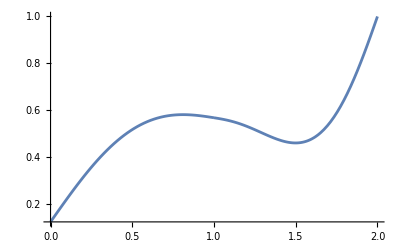

```mathematica
Show[p0,p1,PlotRange->All]
```

```mathematica
points=Import["C:\\Users\\deber\\GeometricTools\\GTL\\UnitTests\\Mathematics\\Interpolation\\1D\\HermiteQuintic1Order0Multiple.txt","CSV"];
```

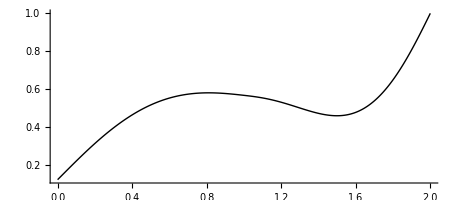

```mathematica
Graphics[Line[points],Axes->True,AspectRatio->Full]
```

```mathematica
p0=Plot[gx,{x,0,1}];
```

```mathematica
p1=Plot[hx,{x,1,2}];
```

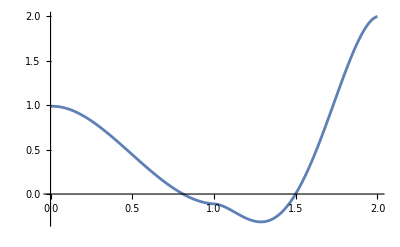

```mathematica
Show[p0,p1,PlotRange->All]
```

```mathematica
points=Import["C:\\Users\\deber\\GeometricTools\\GTL\\UnitTests\\Mathematics\\Interpolation\\1D\\HermiteQuintic1OrderXMultiple.txt","CSV"];
```

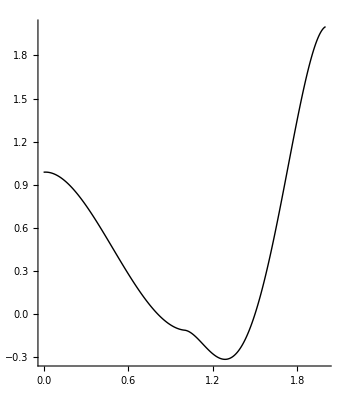

```mathematica
Graphics[Line[points],Axes->True,AspectRatio->Full]
```

```mathematica
p0=Plot[gxx,{x,0,1}];
```

```mathematica
p1=Plot[hxx,{x,1,2}];
```

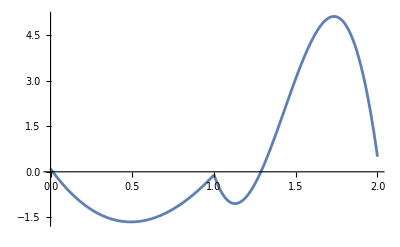

```mathematica
Show[p0,p1,PlotRange->All]
```

```mathematica
points=Import["C:\\Users\\deber\\GeometricTools\\GTL\\UnitTests\\Mathematics\\Interpolation\\1D\\HermiteQuintic1OrderXXMultiple.txt","CSV"];
```

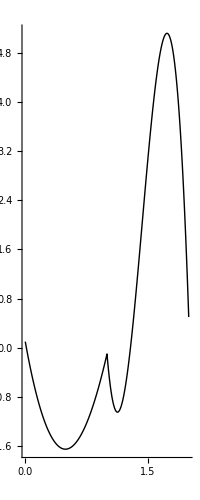

```mathematica
Graphics[Line[points],Axes->True,AspectRatio->Full]
```